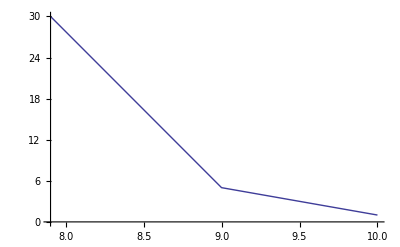

137.316-13.9742 Logν

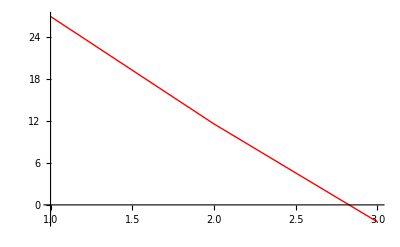

-Graphics-

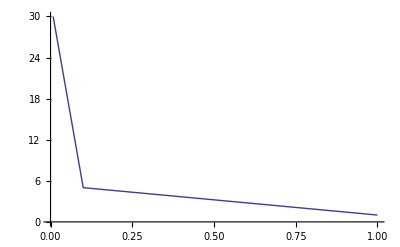

{α→0.0494227,b→11.6379}

```mathematica
sed={{Log[10,80 *10^6],30},{Log[10,1*10^9],5},{Log[10,10*10^9],1}};
sed2={{80 *10^6,30},{1*10^9,5},{10*10^9,1}};
p1=ListLinePlot[sed,PlotStyle->Thick]
s[Logν_]=-α Logν + b /.FindFit[sed,-α Logν + b,{α,b},Logν]
p2=ListLinePlot[s[{Log10[80*10^6],9,10}],PlotStyle->Red]
Show[p1,p2]
ListLinePlot[sed2,PlotStyle->Thick]
FindFit[sed2,b+ν^-α,{α,b},ν]
```

{1.16657×10^-21,{x→5.71036×10^8}}

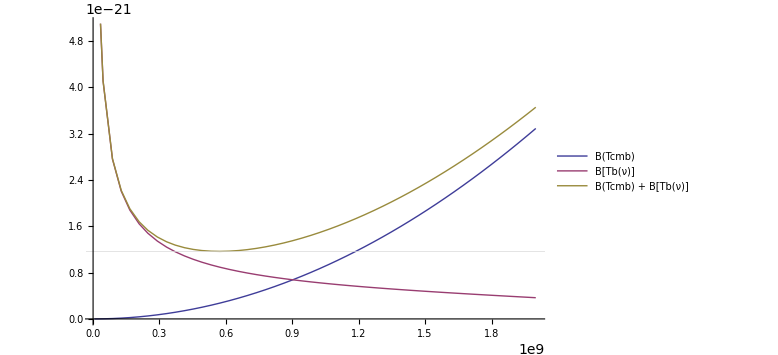

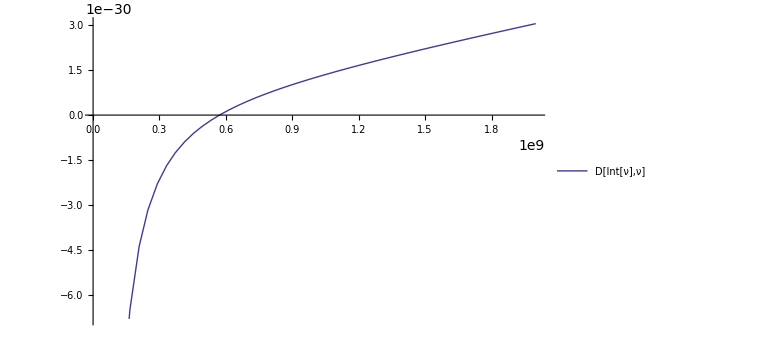

```mathematica
Remove["Global`*"]
h=6.6260755*(10^-34) //N;
k=1.380658*(10^-23) //N;
c=2.99792458*10^8 //N;
tcmb=2.725;
Mhz=10^6;
Ghz=10^9;
Thz=10^12;
tb[nu_]=180((nu/(180 Mhz))^-2.6);
B[T_]=(2 h nu^3)/c^2 1/(Exp[h nu/(k T)]-1);
Int[nu_]=B[tcmb]+B[tb[nu]];
Dint[nu_]=D[Int[nu],nu];
NMinimize[{Int[x],x>10^7},x]
Plot[{B[tcmb],B[tb[nu]],Int[nu]},{nu,6Mhz,2 Ghz},ImageSize->Large,PlotStyle->Thick,AxesStyle->Thick,PlotLegends->{"B(Tcmb)","B[Tb(ν)]","B(Tcmb) + B[Tb(ν)]"},GridLines->{{x/.%[[2]]},{%[[1]]}}]
Plot[Dint[nu],{nu,6Mhz,2 Ghz},ImageSize->Large,PlotStyle->Thick,AxesStyle->Thick,PlotLegends->{"D[Int[ν],ν]"}]
```

```mathematica
NIntegrate[Int[nu],{nu,10 Mhz,Thz}]*4π 6361^2
```

506.046

```mathematica
(h c)/(10^-3 k)
```

14.3877

```mathematica
Remove["Global`*"]
f=Cos[tp]==b/(D+R Cos[t])
g=Cos[t]==√(1-(b/R)^2)
h=b==R Sin[t]
Solve[{f,g,h}]
```

Cos[tp]==b/(D+R Cos[t])

Cos[t]==√(1-b^2/R^2)

b==R Sin[t]

{{Sin[t]→b/R,D→-R √((-b^2+R^2)/R^2)+b Sec[tp],Cos[t]→√(((-b+R) (b+R))/R^2)},{Sin[t]→0,Cos[tp]→0,Cos[t]→1,b→0}}